# Probing the higgs to diphton parameter space (1st run dealing with both k_g and k_γ constraints, no mixing and heavy 2nd stop)

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (11 Jul 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

## Diagram Creation (diphoton)

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

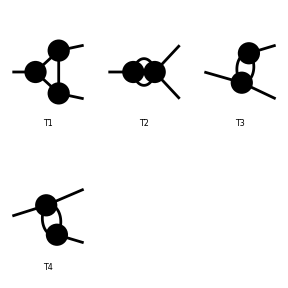

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

loading generic model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 94 particles (incl. antiparticles) in 23 classes

> $CounterTerms are ON

> 383 vertices

classes model {MSSM} initialized

Excluding 0 Generic, 13 Classes, and 50 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 26 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

Restoring 0 Generic, 13 Classes, and 50 Particles fields

Restoring 18 field point(s)

in total: 34 Particles insertions

> Top. 1 ad/becf/dedfef.m, 26 diagrams

> Top. 2 ad/bece/dede.m, 4 diagrams

> Top. 3 ad/becd/eded.m, 2 diagrams

> Top. 4 ad/bdce/eded.m, 2 diagrams

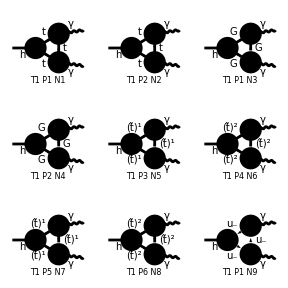

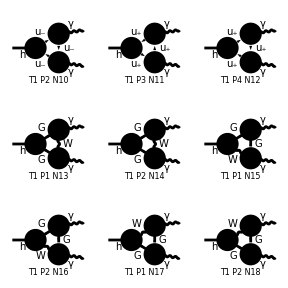

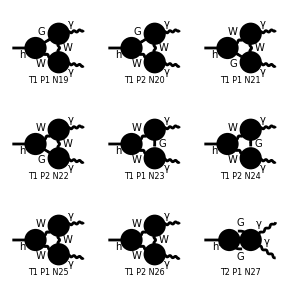

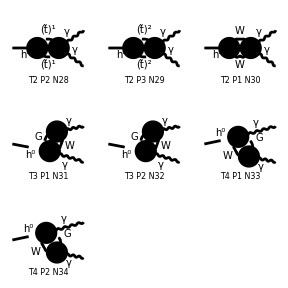

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Model->"MSSM",
ExcludeParticles->{S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],(*S[13,{1,3}],S[13,{2,3}],*)S[14],S[5],F[11],F[12]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 26 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 34 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/parameterSpaceProbes/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][1/(9 CW MW π SB SW)Alfa EL (-Pair1 (Sub5 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]+Sub9 B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]])+12 CA CW MT2 Pair1 (B0i[bb0,0,MT2,MT2]-4 C0i[cc00,0,0,Mh02,MT2,MT2,MT2])+4 Pair1 (Sub5 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+Sub9 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]])-9/4 CW MW2 Pair1 SB (Sub10 B0i[bb0,Mh02,MW2,MW2]-4 Sub10 C0i[cc00,0,0,Mh02,MW2,MW2,MW2]-Mh02 SBA C0i[cc1,0,0,Mh02,MW2,MW2,MW2])-6 CA CW MT2 (Abb3 C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+2 Abb4 C0i[cc2,0,0,Mh02,MT2,MT2,MT2])+9/4 CW MW2 SB (Sub12 C0i[cc0,0,0,Mh02,MW2,MW2,MW2]+2 Sub11 C0i[cc2,0,0,Mh02,MW2,MW2,MW2])-48 CA CW MT2 Pair2 Pair3 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2])+9 CW MW2 Pair2 Pair3 SB Sub10 (C0i[cc12,0,0,Mh02,MW2,MW2,MW2]+C0i[cc22,0,0,Mh02,MW2,MW2,MW2])+4 Pair2 Pair3 Sub5 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])+4 Pair2 Pair3 Sub9 (C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]))]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[1],k[2],0,{}},{V[1],k[3],0,{}}}][0]

0

#### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matDiphoton= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

ColourME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/parameterSpaceProbes/fc-pol-1.frm

running FORM...

ok

Note: polarization sum auto squares the matrix element. Subexpr seems to destroy this line.

```mathematica
SubExprDP[] =SubExpr[];
```

## Diagram Creation (digluon)

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
Paint[topo1];
```

> Top. 1 ad/becf/dedfef.m, 1 diagram

> Top. 2 ad/bece/dede.m, 1 diagram

> Top. 3 ad/becd/eded.m, 1 diagram

> Top. 4 ad/bdce/eded.m, 1 diagram

-Graphics-

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSMQCD.mod

loading classes model file /home/paul/.Mathematica/Applications/FeynArts-3.10/Models/MSSM.mod

> 98 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 403 vertices

classes model {MSSMQCD} initialized

Excluding 0 Generic, 13 Classes, and 50 Particles fields

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 0 Generic, 13 Classes, and 50 Particles fields

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 ad/becf/dedfef.m, 6 diagrams

> Top. 2 ad/bece/dede.m, 2 diagrams

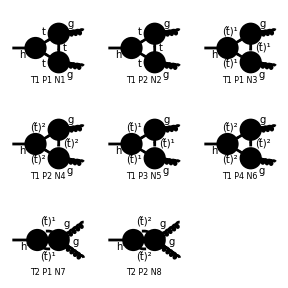

```mathematica
diag1=InsertFields[topo1,{S[1]}->{V[5],V[5]},InsertionLevel->{Particles},Model->"MSSMQCD",
ExcludeParticles->{S[1],S[2],S[11],S[12],S[13,{1,1}],S[13,{2,1}],S[13,{1,2}],S[13,{2,2}],(*S[13,{1,3}],S[13,{2,3}],*)S[14],S[5],F[11],F[12]},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

## Generate Amplitude

```mathematica
ClearProcess[];
amp=CalcFeynAmp[(*OffShell[*)CreateFeynAmp[diag1](*,2-> mg1,3-> mg2]*),FermionChains->Chiral]//Simplify
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 2 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/paul/projects/physics/Research/parameterSpaceProbes/fc-amp-1.frm

running FORM...

ok

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][1/(3 CW MW π SB SW)Alfas EL (1/4 Pair1 (12 CA CW MT2 B0i[bb0,0,MT2,MT2]-Sub5 B0i[bb0,Mh02,MSf2[1,3,3],MSf2[1,3,3]]-Sub9 B0i[bb0,Mh02,MSf2[2,3,3],MSf2[2,3,3]]+4 Sub5 C0i[cc00,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+4 Sub9 C0i[cc00,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]])-3 CA CW MT2 (1/2 Abb1 C0i[cc0,0,0,Mh02,MT2,MT2,MT2]+4 Pair1 C0i[cc00,0,0,Mh02,MT2,MT2,MT2]+Abb2 C0i[cc2,0,0,Mh02,MT2,MT2,MT2]+4 Pair2 Pair3 (C0i[cc12,0,0,Mh02,MT2,MT2,MT2]+C0i[cc22,0,0,Mh02,MT2,MT2,MT2]))+Pair2 Pair3 (Sub5 (C0i[cc12,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc2,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]]+C0i[cc22,0,0,Mh02,MSf2[1,3,3],MSf2[1,3,3],MSf2[1,3,3]])+Sub9 (C0i[cc12,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc2,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]+C0i[cc22,0,0,Mh02,MSf2[2,3,3],MSf2[2,3,3],MSf2[2,3,3]]))) Mat[SUN1]]

#### Check divergent piece

```mathematica
uvcheck=UVDivergentPart[expr]//Simplify;
FreeQ[uvcheck,Divergence]
```

True

```mathematica
UVDivergentPart[amp]//Simplify
divergence=%[[1]]
```

Amp[{{S[1],k[1],Mh0,{}}}→{{V[5,{Glu2}],k[2],0,{√3 ColorCharge}},{V[5,{Glu3}],k[3],0,{√3 ColorCharge}}}][0]

0

### Prepare for looptools

```mathematica
squ=SquaredME[amp];
(* If contains Fermion *)
(*** Don't forget to multiply for FINAL fermions. ***)
squ=(1(squ[[1]]//.squ[[2]]))//.HelicityME[amp]//.{Hel[_]->0}; (* or simply with _Hel=0 *)
(* If contains Colored Particles *)
(*** Don't forget to divide for INITIAL colored particles. ***)

squ=(squ//.ColourME[amp])/1;
(* If contains Vector *)
(*** Don't forget to divide for initial vectors. ***)

matDigluon= PolarizationSum[squ,GaugeTerms->False]/1;  (*Asserting gauge invariance! *)
```

HelicityME::nomat: Warning: No matrix elements to compute.

preparing FORM code in /home/paul/projects/physics/Research/parameterSpaceProbes/fc-pol-1.frm

running FORM...

ok

```mathematica
SubExprDG[] =SubExpr[];
```

```mathematica
oneSig =Polygon[{{0.579,1.310},{0.580,1.287},{0.584,1.269},{0.588,1.253},{0.593,1.238},{0.599,1.225},{0.607,1.211},{0.615,1.196},{0.624,1.182},{0.633,1.167},{0.643,1.154},{0.652,1.142},{0.662,1.131},{0.672,1.120},{0.681,1.110},{0.691,1.100},{0.700,1.091},{0.710,1.082},{0.720,1.074},{0.729,1.066},{0.739,1.058},{0.748,1.051},{0.758,1.044},{0.767,1.036},{0.777,1.030},{0.787,1.024},{0.796,1.017},{0.806,1.011},{0.815,1.006},{0.825,1.000},{0.835,0.995},{0.844,0.989},{0.854,0.984},{0.863,0.980},{0.873,0.976},{0.882,0.971},{0.892,0.967},{0.902,0.963},{0.911,0.960},{0.921,0.956},{0.930,0.953},{0.940,0.950},{0.949,0.947},{0.959,0.945},{0.969,0.944},{0.978,0.943},{0.988,0.941},{0.997,0.940},{1.007,0.941},{1.017,0.942},{1.026,0.944},{1.036,0.947},{1.045,0.953},{1.048,0.964},{1.046,0.975},{1.040,0.992},{1.031,1.007},{1.022,1.020},{1.013,1.034},{1.004,1.046},{0.994,1.058},{0.984,1.070},{0.975,1.081},{0.965,1.092},{0.956,1.103},{0.946,1.113},{0.936,1.124},{0.927,1.134},{0.917,1.144},{0.908,1.154},{0.898,1.164},{0.889,1.174},{0.879,1.184},{0.869,1.194},{0.860,1.203},{0.850,1.213},{0.841,1.222},{0.831,1.231},{0.821,1.240},{0.812,1.249},{0.802,1.258},{0.793,1.267},{0.783,1.275},{0.774,1.283},{0.764,1.290},{0.754,1.298},{0.745,1.305},{0.735,1.312},{0.726,1.320},{0.716,1.326},{0.706,1.333},{0.697,1.339},{0.687,1.345},{0.678,1.351},{0.668,1.356},{0.659,1.360},{0.649,1.363},{0.639,1.365},{0.630,1.367},{0.620,1.366},{0.611,1.364},{0.601,1.360},{0.592,1.350},{0.584,1.333}}];
twoSig=Polygon[{{0.470,1.376},{0.472,1.352},{0.476,1.328},{0.480,1.305},{0.486,1.283},{0.494,1.262},{0.503,1.242},{0.511,1.222},{0.521,1.204},{0.532,1.186},{0.543,1.168},{0.554,1.152},{0.567,1.136},{0.579,1.121},{0.591,1.106},{0.604,1.092},{0.616,1.078},{0.629,1.065},{0.643,1.053},{0.656,1.041},{0.670,1.029},{0.684,1.017},{0.698,1.006},{0.712,0.995},{0.726,0.984},{0.740,0.975},{0.755,0.965},{0.770,0.956},{0.784,0.947},{0.798,0.937},{0.813,0.930},{0.828,0.922},{0.843,0.913},{0.858,0.906},{0.872,0.898},{0.887,0.891},{0.902,0.883},{0.917,0.878},{0.933,0.871},{0.947,0.864},{0.963,0.858},{0.978,0.853},{0.993,0.847},{1.008,0.841},{1.024,0.835},{1.039,0.831},{1.054,0.827},{1.070,0.822},{1.085,0.818},{1.101,0.814},{1.116,0.810},{1.132,0.807},{1.147,0.804},{1.163,0.802},{1.179,0.799},{1.194,0.796},{1.210,0.794},{1.225,0.791},{1.241,0.792},{1.257,0.792},{1.273,0.791},{1.288,0.794},{1.303,0.799},{1.312,0.816},{1.308,0.838},{1.299,0.854},{1.291,0.864},{1.283,0.873},{1.273,0.884},{1.260,0.898},{1.247,0.911},{1.235,0.924},{1.226,0.933},{1.218,0.940},{1.207,0.950},{1.194,0.963},{1.180,0.975},{1.167,0.987},{1.155,1.000},{1.144,1.009},{1.137,1.015},{1.126,1.025},{1.114,1.037},{1.105,1.045},{1.097,1.052},{1.086,1.062},{1.073,1.075},{1.060,1.088},{1.047,1.100},{1.033,1.113},{1.021,1.126},{1.011,1.134},{1.004,1.141},{0.993,1.152},{0.980,1.165},{0.967,1.178},{0.955,1.190},{0.945,1.199},{0.937,1.206},{0.927,1.216},{0.914,1.229},{0.901,1.242},{0.889,1.255},{0.879,1.264},{0.871,1.270},{0.861,1.281},{0.848,1.294},{0.835,1.307},{0.821,1.319},{0.812,1.328},{0.804,1.335},{0.794,1.345},{0.781,1.357},{0.768,1.369},{0.757,1.379},{0.750,1.384},{0.740,1.393},{0.727,1.405},{0.713,1.416},{0.699,1.427},{0.688,1.436},{0.681,1.440},{0.670,1.449},{0.658,1.458},{0.652,1.461},{0.641,1.468},{0.629,1.475},{0.623,1.478},{0.612,1.484},{0.597,1.490},{0.581,1.495},{0.565,1.498},{0.549,1.498},{0.534,1.495},{0.519,1.489},{0.505,1.478},{0.493,1.464},{0.483,1.445},{0.476,1.424},{0.472,1.400}}];
```

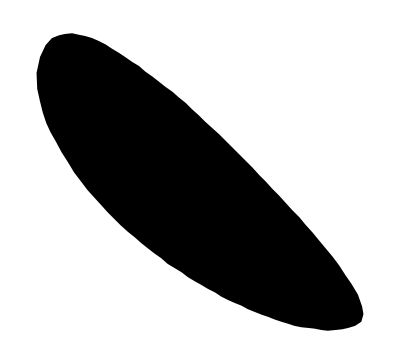

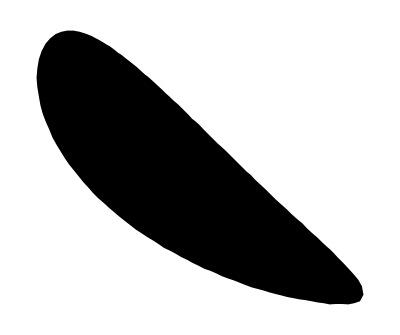

```mathematica
oneSigReg=Region[oneSig]
twoSigReg=Region[twoSig]
```

## Evaluate

```mathematica
Install["LoopTools"]
```

LinkObject[…]

```mathematica
PrependTo[CurrentValue[$FrontEndSession,"NotebookPath"],NotebookDirectory[]];
```

```mathematica
MixedEvalTester[maxSM_,muMass_,betaAng_]:= {VariableValueGeneratro[maxSM,muMass,betaAng],NotebookEvaluate["simDiphotonFull.nb",EvaluationElements->All]}
VariableValueGeneratro[maxSM_,muMass_,betaAng_] :={stopM2 =10000(*RandomReal[{75,maxSM}]*),stopM1 =75+i(* RandomReal[{75,stopM2}]*),offM1 = 0.001(*RandomReal[125]*), offM2=0.001(*RandomReal[(125 - offM1)]*),mixT = 0(* RandomReal[{-((stopM2^2 -stopM1^2)/(2*173)),((stopM2^2 -stopM1^2)/(2*173))}]*),muM = muMass,betaA = betaAng}
```

```mathematica
titleLine = "Run  SM1  SM2  Mixing ResultDP ResultDG  kGamma  kGlue IR1 IR2" ;
titleLine >>"paramProbe2DResults.txt"
```

```mathematica
AbsoluteTiming[For[i=1 , i < 501, i++,MixedEvalTester[1500,250,ArcTan[10]];dataLine = " " <>ToString[i]<>" "<>ToString[stopM1]<>" " <>ToString[stopM2]<>" "<>ToString[mixT]<>(*" "<>ToString[offM1]<> " "<>ToString[offM2]<>*) " "<> ToString[fullResultDP]<> " "<> ToString[fullResultDG]<> " " <> ToString[kGamma]<>" "<> ToString[kGluon]<>" "<> ToString[inRange1]<>" "<> ToString[inRange2];PutAppend[dataLine,"paramProbe2DResults.txt"]]] (*Max stop mass, mu mass, beta angle*)
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

{841.224,Null}

```mathematica
MixedEvalTester[10000,250,1.47]
```

501

{{10000,576,0.001,0.001,0,250,1.47},Null}